{surface0.gpl,surface1.gpl,surface2.gpl,surface3.gpl,surface4.gpl,surface5.gpl,surface6.gpl,surface7.gpl,surface8.gpl,surface9.gpl,surface10.gpl,surface11.gpl,surface12.gpl,surface13.gpl,surface14.gpl,surface15.gpl,surface16.gpl,surface17.gpl,surface18.gpl,surface19.gpl}

/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/FourthOrderSimpleTwoInclusion

{{50,690108},{100,553378},{150,488308},{200,451390},{250,398382},{300,380640},{350,388172},{400,333685},{450,328352},{500,332486},{550,344485},{600,344265},{650,337766},{700,343568},{750,333087},{800,349667},{850,343589},{900,879776},{950,328242},{1000,322086}}

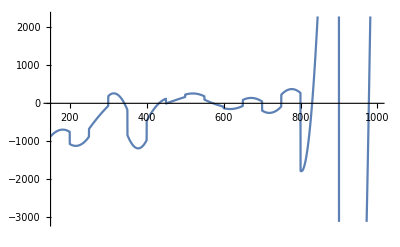

```mathematica
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/FourthOrderSimpleTwoInclusion/gpls"];
ViewSurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
plot1=ListPlot3D[data,BoxRatios->Automatic];
plot2=ListPlot[Transpose[Drop[Transpose[data],-1]], PlotRange -> All];
{plot1,plot2}
]
files= FileNames[];
(*Print[files]*)
numbersInString[s_]:=ToExpression@StringCases[s,NumberString]
files = SortBy[files,numbersInString]
allPlots=Table[ViewSurface[file],{file,files}];
ListAnimate[allPlots]
SolveForce[filename_] :=
Module[{stream, data,force, forcefunction, forceplot, x},
stream = OpenRead[filename];
data = ReadList[stream,{Number,Number}];
Close[stream];
data
]
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/FourthOrderSimpleTwoInclusion"]
Print[SolveForce["energysep.txt"]]
energysepfunc = Interpolation[SolveForce["energysep.txt"]];
forcefunction = energysepfunc';
Plot[forcefunction[x], {x, 150, 1000}]
```

```mathematica
(*{{150,10986.7},{165,11199.5},{180,11312.1},{195,11468.1},{210,11645.7},{225,11821.2},{240,12000},{255,12148.8},{270,12272.7},{285,12448.1},{300,12594.9},{315,12717.7},{330,12847.3},{345,12980.9},{360,13065.7},{375,13193.9},{390,13281.6},{405,13391.8},{420,13469.7},{435,13549.7},{450,13665.9},{465,13733.2},{480,13806.7},{495,13892.3},{510,13969.6},{525,14105.4},{540,14182.4},{555,14239},{570,14312.5},{585,14400.9},{600,14465.7},{615,14501.9},{630,14564.5},{645,14638.1},{660,14708.5},{675,14744.5},{690,14799.5},{705,14842.4},{720,14893.9},{735,14962.1},{750,14992.9},{765,15025.1},{780,15080.3},{795,15105.3},{810,15147.2},{825,15182.3},{840,15205},{855,15269.1},{870,15265.1},{885,15299.6},{900,15355.2},{915,15368.2},{930,15388.2},{945,15418.5},{960,15438},{975,15471},{990,15501.4}}*)
```